```mathematica
expr=g[a,h[b]]
```

g[a,h[b]]

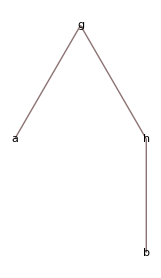

```mathematica
TreeForm[expr]
```

```mathematica
Clear[f];Operate[f,g[{a},b],2]
```

g[{a},b]

```mathematica
?f
```

$Aborted

```mathematica
OwnValues[f]
```

{}

```mathematica
f
```

f

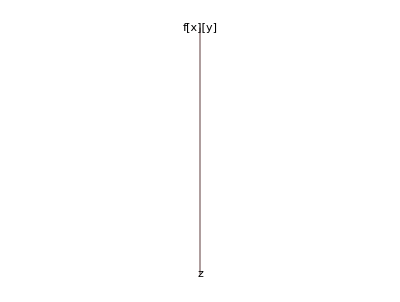

```mathematica
TreeForm[f[x][y][z]]
```

### Positional specification function: MapAt, Insert, Delete, ReplacePart

### Explain the following explaination.

```mathematica
Position[Sqrt[1-u]/Sqrt[1-u^2],Sqrt,Heads->True]
```

{}

### the expression tree form

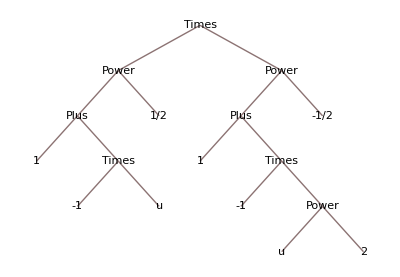

```mathematica
TreeForm[Sqrt[1-u]/Sqrt[1-u^2]]
```

### use the HoldForm

```mathematica
Position[HoldForm[Sqrt[1-u]/Sqrt[1-u^2]],Sqrt,Heads->True]
```

{{1,1,0},{1,2,1,0}}

### use Unevaluated

```mathematica
Position[Unevaluated[Sqrt[1-u]/Sqrt[1-u^2]],Sqrt,Heads->True]
```

{{1,0},{2,1,0}}